```mathematica
ΔiDMdList={0.001,0.01};
chbarval=3*10^8*6.58*10^-25.;
αEMval=1/137.;
<<FeynCalc`;
Do[
modelName[Δ]="Inelastic-dipole-DM-"<>ToString[Δ//N],
{Δ,ΔiDMdList}]
```

FeynCalc 10.1.0 (stable version). For help, use the online documentation, visit the forum and have a look at the supplied examples. The PDF-version of the manual can be downloaded here.

If you use FeynCalc in your research, please evaluate FeynCalcHowToCite[] to learn how to cite this software.

Please keep in mind that the proper academic attribution of our work is crucial to ensure the future development of this package!

## Production

### V->χ_1 χ_0

#### Matrix element of decay V->ee

```mathematica
MprodVll=√(4Pi*αEM)*fVγ*PolarizationVector[pV,μ]*MT[μ,ν]/mV^2 SpinorUBar[pe1,me].GA[ν].SpinorV[pe2,me]//Contract;
MprodVllSquared=(1/3 DoPolarizationSums[FermionSpinSum[MprodVll*ComplexConjugate[MprodVll]]/.{DiracTrace->TR},pV]/.{pe1->pV-pe2}//ExpandScalarProduct)/.{ScalarProduct[pV,pV]->mV^2,ScalarProduct[pe2,pe2]->me^2,ScalarProduct[pe2,pV]->mV^2/2}//Simplify
MprodVllSquaredTimesMomentum[mV_,me_,αEM_]=Quiet[MprodVllSquared*(p/.Solve[2 √(p^2+me^2)==mV,p][[2]])]
```

(16 π αEM fVγ^2 (2 me^2+mV^2))/(3 mV^4)

(8 π αEM fVγ^2 √(mV^2-4 me^2) (2 me^2+mV^2))/(3 mV^4)

#### Matrix element of decay V -> χ_1 χ_0

```mathematica
MprodVχ1χ0=d/4*fVγ(FV[pV,μ]*PolarizationVector[pV,ν]-FV[pV,ν]*PolarizationVector[pV,μ])/mV^2 SpinorUBar[pχ1,mχ1].(GA[μ].GA[ν]-GA[ν].GA[μ]).SpinorV[pχ0,mχ0]//Contract;
MprodVχ1χ0Squared=(1/3 DoPolarizationSums[FermionSpinSum[MprodVχ1χ0*ComplexConjugate[MprodVχ1χ0]]/.{DiracTrace->TR},pV]/.{pχ0->pV-pχ1}//ExpandScalarProduct)/.{ScalarProduct[pV,pV]->mV^2,ScalarProduct[pχ1,pχ1]->mχ1^2,ScalarProduct[pχ1,pV]->(mV^2+mχ1^2-mχ0^2)/2}/.{mχ0->mχ1(1-Δ)}//Expand//Simplify
Normal@Series[MprodVχ1χ0Squared,{Δ,0,0}]
MprodVχ1χ0SquaredTimesMomentum[mV_,Δ_,mχ1_,d_]=Quiet[MprodVχ1χ0Squared*(p/.Solve[√(p^2+mχ1^2)+√(p^2+(mχ1(1-Δ))^2)==mV,p][[2]])]
```

(2 d^2 fVγ^2 (mV^4+(Δ^2-8 Δ+8) mV^2 mχ1^2-2 (Δ-2)^2 Δ^2 mχ1^4))/(3 mV^4)

(2 d^2 fVγ^2 (mV^2+8 mχ1^2))/(3 mV^2)

(d^2 fVγ^2 √(mV^4-2 Δ^2 mV^2 mχ1^2+4 Δ mV^2 mχ1^2-4 mV^2 mχ1^2+Δ^4 mχ1^4-4 Δ^3 mχ1^4+4 Δ^2 mχ1^4) (mV^4+(Δ^2-8 Δ+8) mV^2 mχ1^2-2 (Δ-2)^2 Δ^2 mχ1^4))/(3 mV^5)

#### Branching ratios

```mathematica
massRes["Upsilon"]=9.46;
massRes["Omega"]=0.782;
massRes["Rho0"]=0.775;
massRes["Phi"]=1.019;
massRes["JPsi"]=3.096;
BrRatioLeptons["Upsilon"]=0.0238;
BrRatioLeptons["Omega"]=7.28*10^-5;
BrRatioLeptons["Rho0"]=4.72*10^-5;
BrRatioLeptons["Phi"]=2.954*10^-4.;
BrRatioLeptons["JPsi"]=5.971*10^-2;
mesV=Keys[DownValues@massRes][[All,1,1]]
Do[
BrRatioProcess[V,mχ1_,d_,Δ_]=d^2 If[massRes[V]>mχ1*(2-Δ),Evaluate[BrRatioLeptons[V] MprodVχ1χ0SquaredTimesMomentum[massRes[V],Δ,mχ1,1]/MprodVllSquaredTimesMomentum[massRes[V],0.511*10^-3,αEMval]],0.]
,{V,mesV}]
```

{JPsi,Omega,Phi,Rho0,Upsilon}

-Graphics-

### P->γχ_1 χ_0

```mathematica
Quiet[NotebookEvaluate[FileNameJoin[{NotebookDirectory[]//ParentDirectory//ParentDirectory,"codes/kinematics.nb"}]]];
```

Check that (E^2)_boosted - ((p̄)^2)_boosted = m^2:

Check that (E^2)_boosted - ((p̄)^2)_boosted = m^2 - for the formulas expressed in spherical LLP coordinates:

#### P->γγ

```mathematica
MelementPγγ=(4Pi*αEM)/(16 Pi^2)1/fP*2*1/2*(FV[pγ1,μ]*PolarizationVector[pγ1,ν]-FV[pγ1,ν]*PolarizationVector[pγ1,μ])*(FV[pγ2,α]*PolarizationVector[pγ2,β]-FV[pγ2,β]*PolarizationVector[pγ2,α])*LeviCivita[μ,ν,α,β]//Contract;
MelementPγγSquared=(DoPolarizationSums[DoPolarizationSums[MelementPγγ*ComplexConjugate[MelementPγγ],pγ1,0],pγ2,0]/.{pγ2->pP-pγ1}//ExpandScalarProduct)/.{ScalarProduct[pγ1,pγ1]->0,ScalarProduct[pP,pγ1]->mP^2/2}//Quiet;
ΓPγγ[mP_,αEM_,fP_]=Quiet[1/2 MelementPγγSquared/(8Pi)*(p/.Solve[2p==mP,p][[1]])/mP^2]
```

(αEM^2 mP^3)/(64 π^3 fP^2)

#### P->γχ_1 χ_0

```mathematica
MelementPγχ1χ0=(4Pi*αEM)/(16 Pi^2)1/fP*2*1/2 LeviCivita[μ,ν,α,β](FV[pγ,μ]*PolarizationVector[pγ,ν]-FV[pγ,ν]*PolarizationVector[pγ,μ])1/ScalarProduct[pχ1+pχ0,pχ1+pχ0](FV[pχ1+pχ0,α]*FV[pχ1+pχ0,γ]*MT[β,δ]-FV[pχ1+pχ0,β]*FV[pχ1+pχ0,γ]*MT[α,δ]-FV[pχ1+pχ0,α]*FV[pχ1+pχ0,δ]*MT[β,γ]+FV[pχ1+pχ0,β]*FV[pχ1+pχ0,δ]*MT[α,γ])*d/4 SpinorVBar[pχ1,mχ1].(GA[γ].GA[δ]-GA[δ].GA[γ]).SpinorU[pχ0,mχ0]//ExpandScalarProduct//Contract;
MelementPγχ1χ0Squared=(FermionSpinSum[DoPolarizationSums[MelementPγχ1χ0*ComplexConjugate[MelementPγχ1χ0],pγ,0]]/.{DiracTrace->TR}//ExpandScalarProduct)/.{ScalarProduct[pγ,pγ]->0};
MelementPγχ1χ0SquaredEnergy[mLLP_,E1_,E3_,Δ_,mP_]=MelementPγχ1χ0Squared/.{ScalarProduct[pγ,pχ0]->ProductK1K2energy,ScalarProduct[pγ,pχ1]->ProductK1K3energy,ScalarProduct[pχ0,pχ1]->ProductK2K3energy,ScalarProduct[pχ1,pχ1]->ProductK3K3,ScalarProduct[pχ0,pχ0]->ProductK2K2}/.{m1->0,m2->mLLP(1-Δ),m3->mLLP,m->mP,mχ0->mLLP(1-Δ),mχ1->mLLP}/.{d->1,αEM->1,fP->1};
MelementPγχ1χ0SquaredMandelstam[mLLP_,m12_,m23_,Δ_,mP_,d_,αEM_,fP_]=MelementPγχ1χ0Squared/.{ScalarProduct[pγ,pχ0]->ProductK1K2mandelstam,ScalarProduct[pγ,pχ1]->ProductK1K3mandelstam,ScalarProduct[pχ0,pχ1]->ProductK2K3mandelstam,ScalarProduct[pχ1,pχ1]->ProductK3K3,ScalarProduct[pχ0,pχ0]->ProductK2K2}/.{m1->0,m2->mLLP(1-Δ),m3->mLLP,m->mP,mχ0->mLLP(1-Δ),mχ1->mLLP}//Simplify
ΓPtoγχ1χ0[mP_,mLLP_,Δ_,d_,fP_]:=d^2*If[mP>mLLP(2-Δ),NIntegrate[MelementPγχ1χ0SquaredMandelstam[mLLP,m12,m23,Δ,mP,1,αEMval,fP]/(32*mP^3(2Pi)^3),{m12,m12lower[0,mLLP(1-Δ)],m12upper[mP,mLLP]},{m23,m23lower[m12,mP,0,mLLP(1-Δ),mLLP],m23upper[m12,mP,0,mLLP(1-Δ),mLLP]}],0.]
```

PolarizationSum::notmassless: Warning! You are inserting a polarization sum for massless vector bosons, but the momentum of the external boson pγ is not on-shell. Please put it on-shell via ScalarProduct[pγ,pγ]=0

-1/(π^2 fP^2 m23^2)αEM^2 d^2 (2 m12^2 m23^2+2 m12 m23 (m23^2-m23 ((Δ^2-2 Δ+2) mLLP^2+mP^2)-(Δ-2) Δ mLLP^2 mP^2)+mLLP^2 (-(Δ-2)^2 m23^3+m23^2 ((Δ^4-4 Δ^3+6 Δ^2-4 Δ+2) mLLP^2+2 (3-2 Δ) mP^2)+m23 mP^2 (2 (Δ-2) Δ mLLP^2+(Δ^2-2) mP^2)+(Δ-2)^2 Δ^2 mLLP^2 mP^4))

#### Branching ratios and squared matrix elements

{Eta,EtaPr,Pi0}

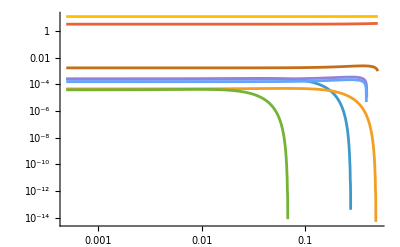

```mathematica
massResP["Pi0"]=0.135;
massResP["Eta"]=0.547;
massResP["EtaPr"]=0.958;
mesP=Keys[DownValues@massResP][[All,1,1]]
{BrPγγ["Pi0"],BrPγγ["Eta"],BrPγγ["EtaPr"]}={0.98823,0.3936,0.02307};
fPtest=1.;
Do[
ΓPγγ[P]=ΓPγγ[massResP[P],αEMval,fPtest];
,{P,mesP}]
Do[
Do[
ΓPtoγXfinalTab[P,Δ]=ParallelTable[{mLLP,ΓPtoγχ1χ0[massResP[P],mLLP,Δ,1,fPtest]},{mLLP,0.,(massResP[P])/2,(massResP[P])/(2*100)}];
ΓPtoγXfinal[P,mLLP_,d_,Δ]=d^2 If[massResP[P]>mLLP(2-Δ),Evaluate[Interpolation[ΓPtoγXfinalTab[P,Δ],InterpolationOrder->1][mLLP]],0.];
BrRatioProcess[P,mLLP_,d_,Δ]=BrPγγ[P]/ΓPγγ[P]*ΓPtoγXfinal[P,mLLP,d,Δ]
,{Δ,ΔiDMdList}]
,{P,mesP}]
LogLogPlot[Evaluate[BrRatioProcess[#,mLLP,1,0.001]&/@Join[mesP,mesV]],{mLLP,0,0.5}]
```

### Exporting

```mathematica
allProcs=Join[mesP,mesV];
listBrRatios[mLLP_,μ_]=Table[{modelName[Δ],Δ,Table[{proc,μ^2 BrRatioProcess[proc,mLLP,1.,Δ]},{proc,allProcs}]},{Δ,ΔiDMdList}];
listSquaredMatrixElements[mLLP_,E1_,E3_]=Table[{modelName[Δ],Table[{proc,MelementPγχ1χ0SquaredEnergy[mLLP,E1,E3,Δ,massResP[proc]]//Expand//Simplify//Together//N},{proc,mesP}]},{Δ,ΔiDMdList}];
Export[FileNameJoin[{NotebookDirectory[],"Production probabilities","BrRatiosProduction.mx"}],listBrRatios[mLLP,μ],"MX"]
Export[FileNameJoin[{NotebookDirectory[],"Production probabilities","SquaredMatrixElements.mx"}],listSquaredMatrixElements[mLLP,E1,E3],"MX"]
```

C:\Users\miksi\Dropbox\Science 2\HNL and scalar phenomenology\_SensCalc\phenomenology\Inelastic-dipole-DM\Production probabilities\BrRatiosProduction.mx

C:\Users\miksi\Dropbox\Science 2\HNL and scalar phenomenology\_SensCalc\phenomenology\Inelastic-dipole-DM\Production probabilities\SquaredMatrixElements.mx

## Decay

-Graphics-

```mathematica
Mdec=μ/4(FV[pγ,μ]*PolarizationVector[pγ,ν]-FV[pγ,ν]*PolarizationVector[pγ,μ])*SpinorUBar[pχ0,mχ0].(GA[μ].GA[ν]-GA[ν].GA[μ]).SpinorU[pχ1,mχ1]//Contract;
MdecSquared=(1/2 DoPolarizationSums[FermionSpinSum[Mdec*ComplexConjugate[Mdec]]/.{DiracTrace->TR},pγ,0]/.{pχ0->pχ1-pγ}//ExpandScalarProduct)/.{ScalarProduct[pγ,pχ1]->(mχ1^2-mχ0^2)/2,ScalarProduct[pγ,pγ]->0}
Γdec[mχ1_,μ_,Δ_]=MdecSquared/(8Pi)*(p/.Solve[p+√(p^2+mχ0^2)==mχ1,p][[1]])/mχ1^2/.{mχ0->mχ1(1-Δ)}//Simplify
Normal@Series[Γdec[mχ1,μ,Δ],{Δ,0,3}]
Export[FileNameJoin[{NotebookDirectory[],"decay widths","ctau.mx"}],Table[{modelName[Δ],Δ,"Default",chbarval/Γdec[mLLP,μ,Δ]},{Δ,ΔiDMdList}],"MX"]
```

PolarizationSum::notmassless: Warning! You are inserting a polarization sum for massless vector bosons, but the momentum of the external boson pγ is not on-shell. Please put it on-shell via ScalarProduct[pγ,pγ]=0

2 μ^2 (mχ1^2-mχ0^2)^2

Solve::nongen: There may be values of the parameters for which some or all solutions are not valid.

-((Δ-2)^3 Δ^3 μ^2 mχ1^3)/(8 π)

(Δ^3 μ^2 mχ1^3)/π

C:\Users\miksi\Dropbox\Science 2\HNL and scalar phenomenology\_SensCalc\phenomenology\Inelastic-dipole-DM\decay widths\ctau.mx

## Elastic scattering

### Kinematics

```mathematica
Print["CM momentum of f χ pair in terms of χ lab energy:"]
vframe[pχ_,Eχ_,mf_]=v/.Solve[pχ-v*Eχ==mf*v,v][[1]];
PCM[Eχ_,mf_,mχ_]=Assuming[Eχ>mχ>0 && mf >0,Simplify[Together[(mf*vframe[pχ,Eχ,mf])/Sqrt[1-vframe[pχ,Eχ,mf]^2]/.pχ->Sqrt[Eχ^2-mχ^2]]]]
Ecm[p_,mf_,mχ_]=Sqrt[p^2+mf^2]+Sqrt[p^2+mχ^2];
Print["Maximal recoil fermion energy:"]
Q2[Ef_,mf_]=2*mf*(Ef-mf);
Efmax[Eχ_,mχ_,mf_]=Assuming[Eχ>me>0 && mf >0,Ee/.Simplify[Solve[Q2[Ee,mf]==4*PCM[Eχ,mf,mχ]^2,Ee]][[1]]]
θSol[q2_,p_]=2*ArcSin[Sqrt[q2]/(2*p)];
Cosθ[q2_,p_]=1-2*q2/(4*p^2);
Cos2θ[q2_,p_]=(1-2*q2/(2*p)^2)^2-1;
Sinθ[q2_,p_]=2*Sqrt[q2]/(2*p)*Sqrt[1-q2/(4*p^2)];
JacobianθToq2[q2_,p_]=D[θSol[q2,p],q2];
Jacobianq2toEf[Ef_,mf_]=D[Q2[Ef,mf],Ef];
```

CM momentum of f χ pair in terms of χ lab energy:

mf √((Eχ^2-mχ^2)/(2 Eχ mf+mf^2+mχ^2))

Maximal recoil fermion energy:

(mf (2 Eχ^2+2 Eχ mf+mf^2-mχ^2))/(2 Eχ mf+mf^2+mχ^2)

### Scattering cross-section

```mathematica
(*Matrix element of the scattering. Neglect the mass splitting - it is irrelevant*)
MScattering=μ/4 SpinorUBar[k1,mχ].(GA[μ].GA[ν]-GA[ν].GA[μ]).SpinorU[p1,mχ]*(FV[p1-k1,μ]*MT[ν,α]-FV[p1-k1,ν]*MT[μ,α])/ScalarProduct[p1-k1,p1-k1]*√(4Pi*αEM)SpinorUBar[k2,mf].GA[α].SpinorU[p2,mf]//Contract;
MScatteringStar=MScattering//ComplexConjugate;
Print["Squared matrix element of the scattering:"];
(*1/4 for the polarization averaging*)
MScatteringSquared[θ_,p_,mχ0_,mf_,μ_]=((1/4 FermionSpinSum[MScattering MScatteringStar]/.DiracTrace->TR//Contract//Simplify)/.{ScalarProduct[p1,p2]->Sqrt[p^2+mχ^2]*Sqrt[p^2+mf^2]+p^2,ScalarProduct[p1,k1]->Sqrt[p^2+mχ^2]*Sqrt[p^2+mχ^2]-p^2*Cos[θ],ScalarProduct[p1,k2]->Sqrt[p^2+mχ^2]*Sqrt[p^2+mf^2]+p*p*Cos[θ],ScalarProduct[p2,k1]->Sqrt[p^2+mf^2]*Sqrt[p^2+mχ^2]+p*p*Cos[θ],ScalarProduct[p2,k2]-> Sqrt[p^2+mf^2]*Sqrt[p^2+mf^2]-p*p*Cos[θ],ScalarProduct[k1,k2]->Sqrt[p^2+mf^2]*Sqrt[p^2+mχ^2]+p^2,ScalarProduct[p1,p1]->mχ^2,ScalarProduct[p2,p2]->mf^2,ScalarProduct[k1,k1]->mχ^2,ScalarProduct[k2,k2]->mf^2}//Simplify//TrigReduce)
(*F is the EM form-factor*)
dsigmadθ[θ_,p_,mχ_,mf_,μ_,F_] = Sin[θ]/(64*Pi^2*Ecm[p,mf,mχ]^2)2*Pi*MScatteringSquared[θ,p,mχ,mf,μ]*F^2;
Print["dσ/dE_f:"]
dσdEfTemp[Ef_,Eχ_,mχ_,mf_,μ_,F_]=Assuming[Eχ>mχ>0&&mf>0&&Eχ>mf,Simplify[dsigmadθ[θ,PCM[Eχ,mf,mχ],mχ,mf,μ,F]*JacobianθToq2[Q2[Ef,mf],PCM[Eχ,mf,mχ]]*Jacobianq2toEf[Ef,mf]/.{Cos[θ]->Cosθ[Q2[Ef,mf],PCM[Eχ,mf,mχ]],Sin[θ]->Sinθ[Q2[Ef,mf],PCM[Eχ,mf,mχ]]}]]//Simplify
Print["Integrated total cross-section:"]
dσdEfTempElectrons[Ee_,Eχ_,mχ_,me_,μ_]=dσdEfTemp[Ee,Eχ,mχ,me,μ,1]//Simplify;
σThresholdElectrons[Eχ_,mχ_,μ_,αEM_,Emin_,me_]=((Integrate[dσdEfTempElectrons[Ee,Eχ,mχ,me,μ],Ee]/.{Ee->Efmax[Eχ,mχ,me] })-(Integrate[dσdEfTempElectrons[Ee,Eχ,mχ,me,μ],Ee]/.{Ee->Emin})//Expand//Simplify)/.{Log[(2 me (Eχ^2-mχ^2))/(2 Eχ me+me^2+mχ^2)]->Log[((2 me (Eχ^2-mχ^2))/(2 Eχ me+me^2+mχ^2))/(Emin-me)],Log[Emin-me]->0}//Simplify
Limit[σThresholdElectrons[Eχ,mχ,μ,αEM,Emin,me],Emin->me]
ME=0.511*10^-3;
MP=0.938;
αEMval=1/137.;
GeVm2Tom2=(2.*10^-16)^2;
Pscattering[Zdet_,nA_,Δzdet_,Emin_,Eχ_,mχ_,μ_]=Zdet*nA*Δzdet*GeVm2Tom2*σThresholdElectrons[Eχ,mχ,μ,αEMval,Emin,ME]
```

Squared matrix element of the scattering:

-(16 (2 π αEM μ^2 mf^2+2 π αEM μ^2 cos(θ) √(mf^2+p^2) √(mχ^2+p^2)+2 π αEM μ^2 √(mf^2+p^2) √(mχ^2+p^2)-π αEM μ^2 mχ^2 cos(θ)+3 π αEM μ^2 mχ^2+2 π αEM μ^2 p^2 cos(θ)+2 π αEM μ^2 p^2))/(cos(θ)-1)

dσ/dE_f:

(αEM F^2 μ^2 (Ef (mχ^2-2 Eχ mf)+mf (2 Eχ^2+2 Eχ mf-3 mχ^2)))/(2 mf (Ef-mf) (Eχ^2-mχ^2))

Integrated total cross-section:

1/2 αEM μ^2 (((2 Eχ me-mχ^2) (Emin (2 Eχ me+me^2+mχ^2)-me (2 Eχ^2+2 Eχ me+me^2-mχ^2)))/(me (Eχ^2-mχ^2) (2 Eχ me+me^2+mχ^2))+2 log((2 me (Eχ^2-mχ^2))/((Emin-me) (2 Eχ me+me^2+mχ^2))))

αEM μ^2 ∞

1.45985×10^-34 Δzdet μ^2 nA Zdet ((1956.95 (0.001022 Eχ-mχ^2) (Emin (0.001022 Eχ+mχ^2+2.61121×10^-7)-0.000511 (2 Eχ^2+0.001022 Eχ-mχ^2+2.61121×10^-7)))/((Eχ^2-mχ^2) (0.001022 Eχ+mχ^2+2.61121×10^-7))+2 log((0.001022 (Eχ^2-mχ^2))/((Emin-0.000511) (0.001022 Eχ+mχ^2+2.61121×10^-7))))

```mathematica
(*Pdecay[mχ_,μ_,Δ_,Eχ_,zmin_,zmax_]=Exp[-zmin/(chbarval/(Normal@Series[Γdec[mχ,μ,Δ],{Δ,0,3}])Eχ/mχ)]-Exp[-zmax/(chbarval/(Normal@Series[Γdec[mχ,μ,Δ],{Δ,0,3}])Eχ/mχ)]
μval=10^-4.;
mχval=1.3;
{NpotGivenExperiment*(Sum[ProbMother[prod]*PmotherToLLP[mχval,μval,prod,FacilityGivenExperiment]*If[Min[ϵGeomTabs[prod][[All,1]]]<mχ<Max[ϵGeomTabs[prod][[All,1]]],Evaluate[Interpolation[ϵGeomTabs[prod][[All,{1,5}]],InterpolationOrder->1][mχ]],0.],{prod,ProductionList}]*Pdecay[mχ,μval,10^-3,Eχ,zminExp,zmaxExp])/.{mχ->mχval,Eχ->200},Sum[NeventsDiscret[mχval,prod,{μval}][[-1]][[-1]],{prod,ProductionList}],NpotGivenExperiment*(Sum[ProbMother[prod]*PmotherToLLP[mχ,μval,prod,FacilityGivenExperiment]*If[Min[ϵGeomTabs[prod][[All,1]]]<mχ<Max[ϵGeomTabs[prod][[All,1]]],Evaluate[Interpolation[ϵGeomTabs[prod][[All,{1,2}]],InterpolationOrder->1][mχ]],0.],{prod,ProductionList}]*Pscattering[82.,nAtomsMaterial[82.],Δzdet,1.,Eχ,mχ,μval])/.{mχ->mχval,Eχ->100}}//Simplify*)
```